### Complex permittivity in real space

```mathematica
Assuming[{a∈Reals,a>0,mD∈Reals,mD>0,r∈Reals,r>0},Integrate[p^4/(p^2+mD^2)Exp[-a p]Sinc[p r],{p,0,∞}]]/.a->0//FullSimplify
```

(mD^2 (-ⅈ Cosh[mD r] (Log[-ⅈ mD r]-Log[ⅈ mD r])+π Sinh[mD r]))/(2 r)

```mathematica
Assuming[{mD∈Reals,mD>0,r∈Reals,r>0},Integrate[(p^3 mD^2)/((p^2+mD^2)^2)Sinc[p r],{p,0,∞}]]//FullSimplify
```

(mD √π MeijerG[{{-1/2},{}},{{1/2,1/2},{0}},(mD^2 r^2)/4])/(2 r)

```mathematica
mD=0.15;
```

```mathematica
ϵ[r_]:=(mD^2 (-ⅈ Cosh[mD r] (Log[-ⅈ mD r]-Log[ⅈ mD r])+π Sinh[mD r]))/(2 r)+ⅈ(mD √π MeijerG[{{-1/2},{}},{{1/2,1/2},{0}},(mD^2 r^2)/4])/(2 r);
```

```mathematica
ϵp[p_]:=p^2/(p^2+mD^2)-ⅈ π (p mD^2)/((p^2+mD^2)^2);
```

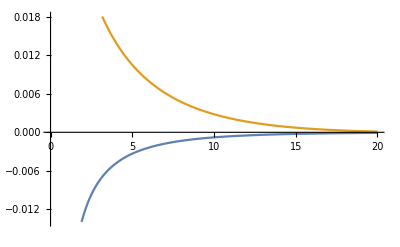

```mathematica
Plot[{Re[ϵ[x]],Im[ϵ[x]]},{x,0,20}]
```

## Discretization

```mathematica
rmax=50.;
dr=0.01;
rlist=Range[dr,rmax,dr];
len=Length[rlist];
```

```mathematica
one[n_,d_]:=DiagonalMatrix[1+0 Range[n-Abs[d]],d];
stringopgauss=(one[len,-1]-2 one[len,0]+one[len,1]);
colopgauss=1/dr^2(one[len,-1]-2 one[len,0]+one[len,1])-2/dr(one[len,-1]+one[len,1]);
```

```mathematica
{vals,vecs}=Eigensystem[N[stringopgauss]];
```

```mathematica
U=Transpose[vecs];
```

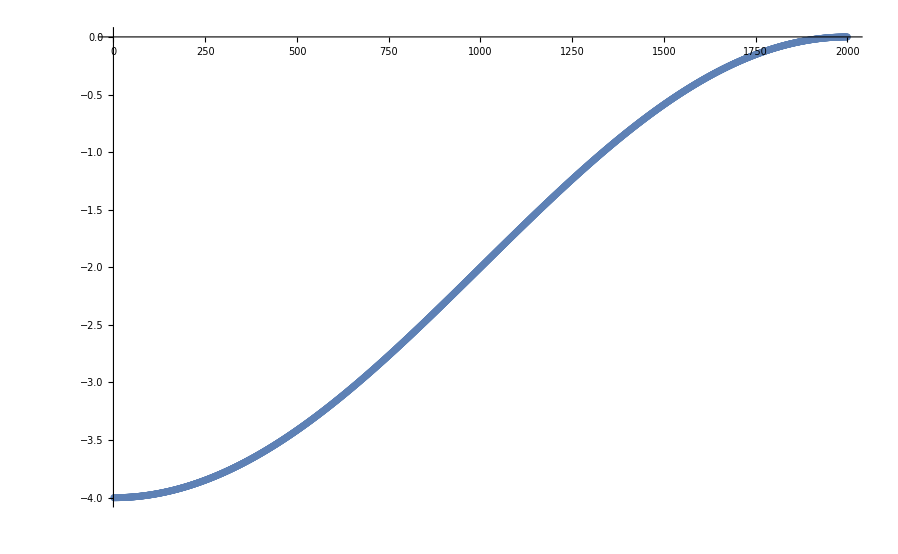

```mathematica
ListPlot[vals]
```

```mathematica
deltatrans=Inverse[U].Array[KroneckerDelta,{len,len}].U;
```

```mathematica
deltatrans[[;;10,;;10]]//MatrixForm
```

(1. | -4.32597×10^-17 | 5.46438×10^-17 | 1.57426×10^-16 | 2.90133×10^-16 | -8.45678×10^-17 | 2.39826×10^-16 | -1.68268×10^-16 | -4.90059×10^-17 | 1.06252×10^-16
-1.11239×10^-16 | 1. | -2.67581×10^-16 | -1.15359×10^-16 | -9.97466×10^-17 | 1.66533×10^-16 | 2.86229×10^-17 | 4.42354×10^-17 | 1.50054×10^-16 | -1.8735×10^-16
-7.37257×10^-17 | 3.07913×10^-17 | 1. | 1.69136×10^-16 | 8.32667×10^-17 | 2.32453×10^-16 | -7.28584×10^-17 | -1.89085×10^-16 | 3.1225×10^-17 | 3.98986×10^-17
8.08815×10^-17 | 4.59702×10^-17 | -2.1684×10^-16 | 1. | -5.72459×10^-17 | 7.28584×10^-17 | 1.38778×10^-17 | -1.21431×10^-17 | -3.29597×10^-16 | -1.47451×10^-16
1.05384×10^-16 | 1.07553×10^-16 | -1.25767×10^-16 | -1.73472×10^-16 | 1. | 1.00614×10^-16 | -1.50921×10^-16 | 2.08167×10^-17 | 2.08167×10^-17 | 4.16334×10^-17
-2.60209×10^-17 | 3.29597×10^-17 | 3.1225×10^-17 | 2.25514×10^-17 | -1.8735×10^-16 | 1. | -9.71445×10^-17 | 2.04697×10^-16 | 1.249×10^-16 | -7.97973×10^-17
7.28584×10^-17 | 1.29237×10^-16 | -4.68375×10^-17 | -5.37764×10^-17 | -2.25514×10^-17 | 7.63278×10^-17 | 1. | 1.04083×10^-17 | 1.35308×10^-16 | 1.66533×10^-16
-4.94396×10^-17 | -1.8735×10^-16 | 1.56125×10^-17 | -3.1225×10^-17 | 1.38778×10^-17 | 1.63064×10^-16 | -1.38778×10^-17 | 1. | 3.46945×10^-18 | -1.52656×10^-16
4.77049×10^-17 | -6.85216×10^-17 | -1.49186×10^-16 | 6.41848×10^-17 | -1.2837×10^-16 | 5.89806×10^-17 | -1.80411×10^-16 | 1.38778×10^-16 | 1. | -2.25514×10^-16
-4.29344×10^-17 | 6.41848×10^-17 | -3.1225×10^-17 | 1.249×10^-16 | 3.81639×10^-17 | 2.08167×10^-17 | -6.59195×10^-17 | 1.11022×10^-16 | -2.08167×10^-16 | 1.)

```mathematica
ϵdis=DiagonalMatrix[Table[ϵ[r],{r,dr,rmax,dr}]];
```

```mathematica
ϵdistra=Inverse[U].ϵdis.U;
```

```mathematica
ϵdistra1=U.ϵdis.Inverse[U];
```

```mathematica
ϵdistra[[;;10,;;10]]//MatrixForm
```

(-0.00146953+0.00442974 ⅈ | -0.0014631+0.00392421 ⅈ | 0.00108758-0.00219177 ⅈ | 0.000850564-0.00132663 ⅈ | -0.000688219+0.000863331 ⅈ | 0.000579548-0.000611518 ⅈ | 0.000498112-0.000449632 ⅈ | -0.000437747+0.000347716 ⅈ | 0.000389451-0.000274194 ⅈ | 0.00035131-0.000223558 ⅈ
-0.0014631+0.00392421 ⅈ | -0.00255711+0.0066215 ⅈ | 0.00231366-0.00525084 ⅈ | 0.0017758-0.0030551 ⅈ | -0.00143011+0.00193814 ⅈ | 0.00118633-0.00131296 ⅈ | 0.0010173-0.000959234 ⅈ | -0.000887563+0.000723826 ⅈ | 0.000789058-0.000571274 ⅈ | 0.000708921-0.000458486 ⅈ
0.00108758-0.00219177 ⅈ | 0.00231366-0.00525084 ⅈ | -0.00324533+0.00748484 ⅈ | -0.00289321+0.00586235 ⅈ | 0.00227391-0.00350473 ⅈ | -0.00186786+0.00228586 ⅈ | -0.00157578+0.00158716 ⅈ | 0.00136861-0.00118279 ⅈ | -0.00120703+0.000908118 ⅈ | -0.00108231+0.000726885 ⅈ
0.000850564-0.00132663 ⅈ | 0.0017758-0.0030551 ⅈ | -0.00289321+0.00586235 ⅈ | -0.00374344+0.00793447 ⅈ | 0.00333096-0.00621007 ⅈ | -0.00266336+0.00377892 ⅈ | -0.00221917+0.00250942 ⅈ | 0.00189525-0.00177145 ⅈ | -0.00166186+0.0013384 ⅈ | -0.00147775+0.00104037 ⅈ
-0.000688219+0.000863331 ⅈ | -0.00143011+0.00193814 ⅈ | 0.00227391-0.00350473 ⅈ | 0.00333096-0.00621007 ⅈ | -0.0041329+0.00820866 ⅈ | 0.00368227-0.00643363 ⅈ | 0.00298283-0.00396322 ⅈ | -0.00251242+0.00266503 ⅈ | 0.00216597-0.0019037 ⅈ | 0.00191347-0.00145288 ⅈ
0.000579548-0.000611518 ⅈ | 0.00118633-0.00131296 ⅈ | -0.00186786+0.00228586 ⅈ | -0.00266336+0.00377892 ⅈ | 0.00368227-0.00643363 ⅈ | -0.00445237+0.00839295 ⅈ | -0.00397552+0.00658924 ⅈ | 0.00325355-0.00409547 ⅈ | -0.00276404+0.00277951 ⅈ | -0.00240081+0.00200319 ⅈ
0.000498112-0.000449632 ⅈ | 0.0010173-0.000959234 ⅈ | -0.00157578+0.00158716 ⅈ | -0.00221917+0.00250942 ⅈ | 0.00298283-0.00396322 ⅈ | -0.00397552+0.00658924 ⅈ | -0.00472309+0.00852521 ⅈ | 0.00422714-0.00670372 ⅈ | -0.00348839+0.00419496 ⅈ | -0.00298434+0.00286723 ⅈ
-0.000437747+0.000347716 ⅈ | -0.000887563+0.000723826 ⅈ | 0.00136861-0.00118279 ⅈ | 0.00189525-0.00177145 ⅈ | -0.00251242+0.00266503 ⅈ | 0.00325355-0.00409547 ⅈ | 0.00422714-0.00670372 ⅈ | -0.00495792+0.00862469 ⅈ | 0.00444744-0.00679144 ⅈ | 0.00369573-0.00427249 ⅈ
0.000389451-0.000274194 ⅈ | 0.000789058-0.000571274 ⅈ | -0.00120703+0.000908118 ⅈ | -0.00166186+0.0013384 ⅈ | 0.00216597-0.0019037 ⅈ | -0.00276404+0.00277951 ⅈ | -0.00348839+0.00419496 ⅈ | 0.00444744-0.00679144 ⅈ | -0.00516526+0.00870223 ⅈ | -0.00464335+0.00686079 ⅈ
0.00035131-0.000223558 ⅈ | 0.000708921-0.000458486 ⅈ | -0.00108231+0.000726885 ⅈ | -0.00147775+0.00104037 ⅈ | 0.00191347-0.00145288 ⅈ | -0.00240081+0.00200319 ⅈ | -0.00298434+0.00286723 ⅈ | 0.00369573-0.00427249 ⅈ | -0.00464335+0.00686079 ⅈ | -0.00535085+0.00876434 ⅈ)

```mathematica
ϵdis1=ParallelTable[ϵ[r],{r,dr,rmax,dr}];
```

```mathematica
ϵdisp1=Fourier[ϵdis1];
```

```mathematica
ϵdisp=ParallelTable[ϵp[p],{p,-1,1,0.001}];
```

```mathematica
ϵdisp2=Fourier[ϵdisp]
```

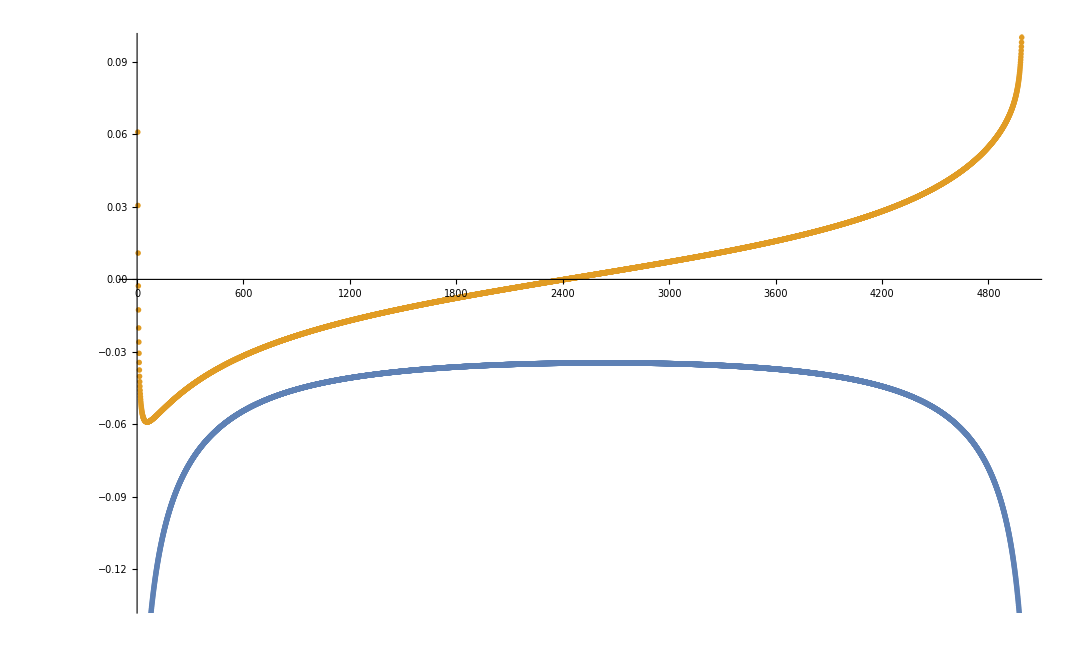

```mathematica
ListPlot[{Re[ϵdisp1],Im[ϵdisp1]}]
```

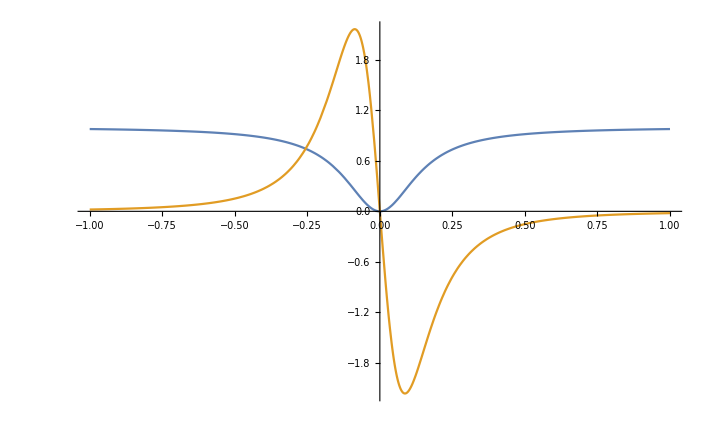

```mathematica
Plot[{p^2/(p^2+mD^2),-(p mD^2)/((p^2+mD^2)^2)},{p,-1,1}]
```